```mathematica
PlotCondition[cond_, size_:10] :=RegionPlot[cond, {x, -size, size}, {y, -size, size}]



PlotComplex[func_, size_:10,opha_:5,prec_:120,offX_:0,offY_:0] := {n=-4, m=-4,Monitor[
{RegionPlot[True,{x, -size, size}, {y, -size, size},ColorFunction->Function[{x,y},{Hue[Arg[func[(x+offX)+ⅈ*(y+offY)]]/(2π),1,1,1/(1+Abs[func[(x+offX)+ⅈ*(y+offY)]]/opha)],n=y}],ColorFunctionScaling->False,ImageSize -> Large, PlotPoints-> prec],RegionPlot[True,{x, -size, size}, {y, -size, size},ColorFunction->Function[{x,y},{Hue[Arg[x+ⅈ*y]/(2π),1,1,1/(1+Abs[x+ⅈ*y]/opha)],m=y}],ColorFunctionScaling->False,ImageSize -> Large,PlotPoints-> Min[prec,120]]},
Grid[{Text[Style["Calculating Points :",Darker[Blue,0.66]]],ProgressIndicator[n+m,{-2*size,2*size}]},{n,m}]]}
```

```mathematica
f[z_] :=(z)^2
PlotComplex[f,4,1,10]
```

{-4,-4,{-Graphics-,-Graphics-}}

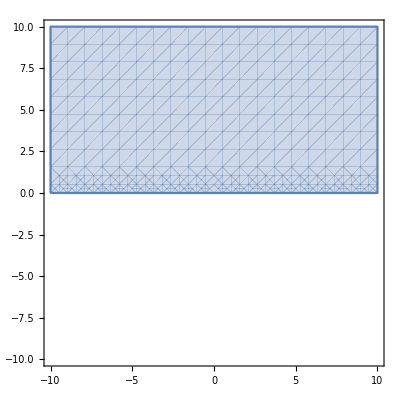

```mathematica
z=x+ⅈ*y;
PlotCondition[Abs[(ⅈ*z+1)/(ⅈ*z-1)]<1,10]
```

```mathematica
FindRoot[x^2-2,{x,1},EvaluationMonitor:>Print["x = ",x " x^2 - 2 =",x^2-2]]
```

x = 1.  x^2 - 2 =-1.

x = 1.5  x^2 - 2 =0.25

x = 1.41667  x^2 - 2 =0.00694444

x = 1.41422  x^2 - 2 =6.0073×10^-6

x = 1.41421  x^2 - 2 =4.51061×10^-12

x = 1.41421  x^2 - 2 =4.44089×10^-16

{x→1.41421}